```mathematica
Quit[]
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
PuntosQ=6
```

6

```mathematica
r[j_]:=(PuntosQ+1-j)/j;
PunInte[i_,j_]:={(Lados[[i,1,1]]+r[j] Lados[[i,2,1]])/(1+r[j]),(Lados[[i,1,2]]+r[j]Lados[[i,2,2]])/(1+r[j])};
```

```mathematica
VerticesP={{0,0},{1,0},{1,1},{0,1}}
```

{{0,0},{1,0},{1,1},{0,1}}

```mathematica
Lados=Table[{VerticesP[[i]],VerticesP[[i Boole[i!=4]+1]]},{i,1,4}]
```

{{{0,0},{1,0}},{{1,0},{1,1}},{{1,1},{0,1}},{{0,1},{0,0}}}

```mathematica
PuntosInt=Table[PunInte[i, j], {i, 1, 4}, {j, 1, PuntosQ}]
```

{{{6/7,0},{5/7,0},{4/7,0},{3/7,0},{2/7,0},{1/7,0}},{{1,6/7},{1,5/7},{1,4/7},{1,3/7},{1,2/7},{1,1/7}},{{1/7,1},{2/7,1},{3/7,1},{4/7,1},{5/7,1},{6/7,1}},{{0,1/7},{0,2/7},{0,3/7},{0,4/7},{0,5/7},{0,6/7}}}

```mathematica
PuntosIn=Table[Insert[{PuntosInt[[i]]},i, 1],{i,1,4}]
```

{{1,{{6/7,0},{5/7,0},{4/7,0},{3/7,0},{2/7,0},{1/7,0}}},{2,{{1,6/7},{1,5/7},{1,4/7},{1,3/7},{1,2/7},{1,1/7}}},{3,{{1/7,1},{2/7,1},{3/7,1},{4/7,1},{5/7,1},{6/7,1}}},{4,{{0,1/7},{0,2/7},{0,3/7},{0,4/7},{0,5/7},{0,6/7}}}}

```mathematica
Pun=PuntosIn
```

{{1,{{6/7,0},{5/7,0},{4/7,0},{3/7,0},{2/7,0},{1/7,0}}},{2,{{1,6/7},{1,5/7},{1,4/7},{1,3/7},{1,2/7},{1,1/7}}},{3,{{1/7,1},{2/7,1},{3/7,1},{4/7,1},{5/7,1},{6/7,1}}},{4,{{0,1/7},{0,2/7},{0,3/7},{0,4/7},{0,5/7},{0,6/7}}}}

```mathematica
FlatPuntosIn=Flatten[ PuntosInt,1]
```

{{6/7,0},{5/7,0},{4/7,0},{3/7,0},{2/7,0},{1/7,0},{1,6/7},{1,5/7},{1,4/7},{1,3/7},{1,2/7},{1,1/7},{1/7,1},{2/7,1},{3/7,1},{4/7,1},{5/7,1},{6/7,1},{0,1/7},{0,2/7},{0,3/7},{0,4/7},{0,5/7},{0,6/7}}

```mathematica
NamePunInt=Table[Callout[{FlatPuntosIn[[i,1]],FlatPuntosIn[[i,2]]}],{i,1,Length[FlatPuntosIn]}];
```

```mathematica
Show[{Graphics[{{EdgeForm[Black],LightRed,Opacity[0.2],Polygon[VerticesP]},(*{Red,PointSize[Large],Point[Pun[[1,2]]]},*)(*{Blue,PointSize[Large],Point[Pun[[2,2]]]},*)(*{Green,PointSize[Large],Point[Pun[[3,2]]]},*)(*{PointSize[Large],Point[Pun[[4,2]]]}*)},Frame->False,ImageSize->Small] ,ListPlot[NamePunInt,AspectRatio->1,ImageSize->Small,PlotStyle->PointSize[Medium]]}]
```

-Graphics-

```mathematica
ProdDis[x_]:=DiscreteUniformDistribution[{1,x}]
```

```mathematica
RandN[x_,y_]:=RandomVariate[ProdDis[x],y];
```

```mathematica
PuntosIn=Pun
VerticesPC=VerticesP
```

{{1,{{6/7,0},{5/7,0},{4/7,0},{3/7,0},{2/7,0},{1/7,0}}},{2,{{1,6/7},{1,5/7},{1,4/7},{1,3/7},{1,2/7},{1,1/7}}},{3,{{1/7,1},{2/7,1},{3/7,1},{4/7,1},{5/7,1},{6/7,1}}},{4,{{0,1/7},{0,2/7},{0,3/7},{0,4/7},{0,5/7},{0,6/7}}}}

{{0,0},{1,0},{1,1},{0,1}}

```mathematica
PDeLados=Table[k,{k,1,4}]
```

{1,2,3,4}

```mathematica
GrafP[t_]:=(
i=RandomChoice[PDeLados];
PDeLados=DeleteCases[PDeLados, i];
PuntosIntwoEdges={PuntosIn[[i,2]],PuntosIn[[i Boole[i!=4]+1 ,2]]} ;
(*Cambiar las dos celdas {PuntosIn[[**,2]],PuntosIn[[**,2]]}*)
NewIPoints1=PuntosIntwoEdges[[1]][[RandN[Length[PuntosIntwoEdges[[1]]],1][[1]];;Length[PuntosIntwoEdges[[1]]]]];(*Cambiar [[RandomInteger[{1,**}];;**]]*)
NewIPoints2=PuntosIntwoEdges[[2]][[1;;RandN[Length[PuntosIntwoEdges[[2]]],1][[1]]]];(*Aqui tambien se debe cambiar*)
PuntosIn[[i,2]]=NewIPoints1;
PuntosIn[[i Boole[i!=4]+1,2]]=NewIPoints2 ;(*Calbiar PuntosIn[[**,2]]*)
VerticesPC[[i Boole[i!=4]+1]]={First[NewIPoints1],Last[NewIPoints2]};
PS=Position[VerticesPC,{{_,_},{_,_}},{1}];
VerticesPCFla=FlattenAt[VerticesPC,PS];
{Graphics[{{EdgeForm[Black],LightGreen,Opacity[0.2],Polygon[VerticesPCFla]},{Red,Point[FlatPuntosIn]}},Frame->True,ImageSize->Tiny],
1/2 Sum[VerticesPCFla[[l,1]]VerticesPCFla[[l+1,2]]-VerticesPCFla[[l+1,1]]VerticesPCFla[[l,2]],{l,1,Length[VerticesPCFla]-1}],Length[DeleteDuplicates[VerticesPCFla]]}
)
```

```mathematica
Multi[k_]:=(
PuntosIn=Pun;
VerticesPC=VerticesP;
PDeLados=Table[t,{t,1,4}];
Table[GrafP[i],{i,1,4}])
```

```mathematica
NumeroDePiedras=20000
```

20000

```mathematica
PFinal=Table[Multi[r],{r,1,NumeroDePiedras}];
```

```mathematica
AreasDP=Table[PFinal[[i,4,2]],{i,1,NumeroDePiedras}];
```

```mathematica
NuAristas=Table[PFinal[[i,4,3]],{i,1,NumeroDePiedras}];
```

```mathematica
Length[AreasDP]
```

20000

```mathematica
Table[PFinal[[i]],{i,1,10}];
```

```mathematica
AreaVsPro=Tally[AreasDP]
```

{{73/98,602},{5/7,706},{40/49,278},{65/98,748},{61/98,717},{31/49,688},{36/49,584},{29/49,616},{75/98,506},{37/49,549},{4/7,592},{25/49,311},{11/14,395},{67/98,722},{9/14,741},{59/98,699},{81/98,239},{27/49,454},{38/49,446},{33/49,701},{34/49,656},{30/49,646},{51/98,408},{22/49,72},{79/98,333},{69/98,695},{71/98,677},{41/49,218},{1/2,346},{85/98,106},{55/98,598},{57/98,676},{26/49,410},{32/49,721},{47/98,162},{53/98,474},{83/98,189},{41/98,49},{24/49,141},{6/7,115},{37/98,15},{39/49,353},{43/49,54},{44/49,16},{45/98,121},{87/98,37},{3/7,32},{43/98,61},{5/14,25},{23/49,115},{18/49,18},{39/98,32},{20/49,48},{15/49,13},{17/49,25},{45/49,4},{29/98,10},{89/98,4},{12/49,4},{19/49,18},{33/98,8},{13/14,1}}

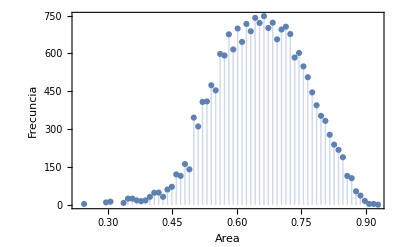

```mathematica
ListPlot[AreaVsPro,Filling->Axis,Frame->True, FrameLabel->{Area,Frecuncia}]
```

```mathematica
AristasVsPro=Tally[NuAristas]
```

{{6,7032},{7,6628},{8,2460},{5,3288},{4,592}}

```mathematica
Sum[AristasVsPro[[i,2]],{i,1,Length[AristasVsPro]}]
```

20000

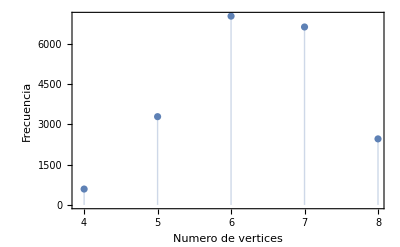

```mathematica
ListPlot[AristasVsPro,Filling->Axis,Frame->True,FrameLabel->{"Numero de  vertices","Frecuencia"}]
```

```mathematica
TotalEvents=Sum[AristasVsPro[[i,2]],{i,1,Length[AristasVsPro]}]
```

20000

```mathematica
DistPro=Table[{AristasVsPro[[i,1]],AristasVsPro[[i,2]]/TotalEvents},{i,1,Length[AristasVsPro]}]//N
```

{{6.,0.3516},{7.,0.3314},{8.,0.123},{5.,0.1644},{4.,0.0296}}

```mathematica
Sum[DistPro[[i,2]],{i,1,Length[DistPro]}]
```

1.

```mathematica
xbins=Range[0.2,1,0.02];
ybins=Range[3.5,8.5,1]
```

{3.5,4.5,5.5,6.5,7.5,8.5}

```mathematica
FinalCuatro=Table[PFinal[[i,4]],{i,1,Length[PFinal]}];
```

```mathematica
XY=Table[{FinalCuatro[[i,2]],FinalCuatro[[i,3]]},{i,1,Length[FinalCuatro]}];
```

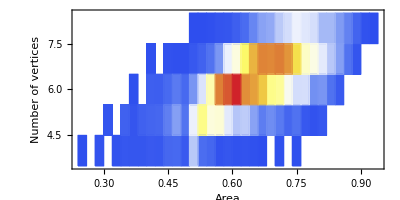

```mathematica
ci=DensityHistogram[XY,{{xbins},{ybins}},ColorFunction->"TemperatureMap",FrameLabel->{Style["Area",12,FontFamily->"Consolas"],Style["Number of vertices",12,FontFamily->"Consolas"]},ChartBaseStyle->EdgeForm[Thin],ChartLegends->Placed[BarLegend[Automatic,15,LegendLabel->Placed[Style["Frequency",12,FontFamily->"Consolas"],Below]],Below],AspectRatio->1/2]
```

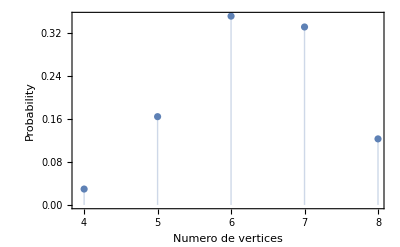

```mathematica
ListPlot[DistPro,Filling->Axis,Frame->True,FrameLabel->{"Numero de  vertices","Probability"}]
```

```mathematica
Hist=HistogramList[XY,{{xbins},{ybins}}]
```

{{{0.2,0.22,0.24,0.26,0.28,0.3,0.32,0.34,0.36,0.38,0.4,0.42,0.44,0.46,0.48,0.5,0.52,0.54,0.56,0.58,0.6,0.62,0.64,0.66,0.68,0.7,0.72,0.74,0.76,0.78,0.8,0.82,0.84,0.86,0.88,0.9,0.92,0.94,0.96,0.98,1.},{3.5,4.5,5.5,6.5,7.5,8.5}},{{0,0,0,0,0},{0,0,0,0,0},{4,0,0,0,0},{0,0,0,0,0},{10,0,0,0,0},{0,13,0,0,0},{8,0,0,0,0},{16,34,0,0,0},{15,14,4,0,0},{15,35,0,0,0},{21,41,30,5,0},{19,45,29,0,0},{45,89,50,9,0},{48,144,80,5,0},{21,67,48,5,0},{211,297,129,19,1},{55,463,263,36,1},{44,380,433,66,5},{9,388,650,131,12},{15,278,686,298,15},{8,205,726,376,30},{10,217,635,490,53},{6,149,614,591,102},{2,84,568,646,149},{0,115,462,641,160},{6,79,450,653,213},{0,43,344,627,247},{4,63,247,538,299},{0,19,250,409,274},{0,9,120,369,250},{0,17,128,282,184},{0,0,64,209,184},{0,0,22,144,138},{0,0,0,66,94},{0,0,0,13,40},{0,0,0,0,8},{0,0,0,0,1},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}}

```mathematica
Hist[[1,1]]//Length
```

41

```mathematica
reco=Table[Row[{Hist[[1,1,i]]," - ",Hist[[1,1,i+1]]}],{i,1,Length[Hist[[1,1]]]-1}]
```

{0.2 - 0.22,0.22 - 0.24,0.24 - 0.26,0.26 - 0.28,0.28 - 0.3,0.3 - 0.32,0.32 - 0.34,0.34 - 0.36,0.36 - 0.38,0.38 - 0.4,0.4 - 0.42,0.42 - 0.44,0.44 - 0.46,0.46 - 0.48,0.48 - 0.5,0.5 - 0.52,0.52 - 0.54,0.54 - 0.56,0.56 - 0.58,0.58 - 0.6,0.6 - 0.62,0.62 - 0.64,0.64 - 0.66,0.66 - 0.68,0.68 - 0.7,0.7 - 0.72,0.72 - 0.74,0.74 - 0.76,0.76 - 0.78,0.78 - 0.8,0.8 - 0.82,0.82 - 0.84,0.84 - 0.86,0.86 - 0.88,0.88 - 0.9,0.9 - 0.92,0.92 - 0.94,0.94 - 0.96,0.96 - 0.98,0.98 - 1.}

```mathematica
seco=Prepend[Table[Row[{Hist[[1,2,i]],"-",Hist[[1,2,i+1]]}],{i,1,Length[Hist[[1,2]]]-1}],"           "]
```

{           ,3.5-4.5,4.5-5.5,5.5-6.5,6.5-7.5,7.5-8.5}

```mathematica
seco=Table[ToString[seco[[i]]],{i,1,Length[seco]}]
```

{           ,3.5-4.5,4.5-5.5,5.5-6.5,6.5-7.5,7.5-8.5}

```mathematica
serti=TableForm[Table[Reverse[Table[Hist[[2,j,i]],{i,1,5}]],{j,1,Length[Hist[[2]]]}],TableDirections->Row,TableHeadings->{reco,seco}]
```

| 0.2 - 0.22 | 0.22 - 0.24 | 0.24 - 0.26 | 0.26 - 0.28 | 0.28 - 0.3 | 0.3 - 0.32 | 0.32 - 0.34 | 0.34 - 0.36 | 0.36 - 0.38 | 0.38 - 0.4 | 0.4 - 0.42 | 0.42 - 0.44 | 0.44 - 0.46 | 0.46 - 0.48 | 0.48 - 0.5 | 0.5 - 0.52 | 0.52 - 0.54 | 0.54 - 0.56 | 0.56 - 0.58 | 0.58 - 0.6 | 0.6 - 0.62 | 0.62 - 0.64 | 0.64 - 0.66 | 0.66 - 0.68 | 0.68 - 0.7 | 0.7 - 0.72 | 0.72 - 0.74 | 0.74 - 0.76 | 0.76 - 0.78 | 0.78 - 0.8 | 0.8 - 0.82 | 0.82 - 0.84 | 0.84 - 0.86 | 0.86 - 0.88 | 0.88 - 0.9 | 0.9 - 0.92 | 0.92 - 0.94 | 0.94 - 0.96 | 0.96 - 0.98 | 0.98 - 1.
            | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 5 | 12 | 15 | 30 | 53 | 102 | 149 | 160 | 213 | 247 | 299 | 274 | 250 | 184 | 184 | 138 | 94 | 40 | 8 | 1 | 0 | 0 | 0
3.5-4.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 9 | 5 | 5 | 19 | 36 | 66 | 131 | 298 | 376 | 490 | 591 | 646 | 641 | 653 | 627 | 538 | 409 | 369 | 282 | 209 | 144 | 66 | 13 | 0 | 0 | 0 | 0 | 0
4.5-5.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 30 | 29 | 50 | 80 | 48 | 129 | 263 | 433 | 650 | 686 | 726 | 635 | 614 | 568 | 462 | 450 | 344 | 247 | 250 | 120 | 128 | 64 | 22 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.5-6.5 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 34 | 14 | 35 | 41 | 45 | 89 | 144 | 67 | 297 | 463 | 380 | 388 | 278 | 205 | 217 | 149 | 84 | 115 | 79 | 43 | 63 | 19 | 9 | 17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.5-7.5 | 0 | 0 | 4 | 0 | 10 | 0 | 8 | 16 | 15 | 15 | 21 | 19 | 45 | 48 | 21 | 211 | 55 | 44 | 9 | 15 | 8 | 10 | 6 | 2 | 0 | 6 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
serti=Table[Table[Hist[[2,j,i]],{i,1,5}],{j,1,Length[Hist[[2]]]}]
```

{{0,0,0,0,0},{0,0,0,0,0},{4,0,0,0,0},{0,0,0,0,0},{10,0,0,0,0},{0,13,0,0,0},{8,0,0,0,0},{16,34,0,0,0},{15,14,4,0,0},{15,35,0,0,0},{21,41,30,5,0},{19,45,29,0,0},{45,89,50,9,0},{48,144,80,5,0},{21,67,48,5,0},{211,297,129,19,1},{55,463,263,36,1},{44,380,433,66,5},{9,388,650,131,12},{15,278,686,298,15},{8,205,726,376,30},{10,217,635,490,53},{6,149,614,591,102},{2,84,568,646,149},{0,115,462,641,160},{6,79,450,653,213},{0,43,344,627,247},{4,63,247,538,299},{0,19,250,409,274},{0,9,120,369,250},{0,17,128,282,184},{0,0,64,209,184},{0,0,22,144,138},{0,0,0,66,94},{0,0,0,13,40},{0,0,0,0,8},{0,0,0,0,1},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
texf=Prepend[Table[Prepend[serti[[i]],ToString[reco[[i]]]],{i,1,Length[Hist[[1,1]]]-1}],seco]
```

{{           ,3.5-4.5,4.5-5.5,5.5-6.5,6.5-7.5,7.5-8.5},{0.2 - 0.22,0,0,0,0,0},{0.22 - 0.24,0,0,0,0,0},{0.24 - 0.26,4,0,0,0,0},{0.26 - 0.28,0,0,0,0,0},{0.28 - 0.3,10,0,0,0,0},{0.3 - 0.32,0,13,0,0,0},{0.32 - 0.34,8,0,0,0,0},{0.34 - 0.36,16,34,0,0,0},{0.36 - 0.38,15,14,4,0,0},{0.38 - 0.4,15,35,0,0,0},{0.4 - 0.42,21,41,30,5,0},{0.42 - 0.44,19,45,29,0,0},{0.44 - 0.46,45,89,50,9,0},{0.46 - 0.48,48,144,80,5,0},{0.48 - 0.5,21,67,48,5,0},{0.5 - 0.52,211,297,129,19,1},{0.52 - 0.54,55,463,263,36,1},{0.54 - 0.56,44,380,433,66,5},{0.56 - 0.58,9,388,650,131,12},{0.58 - 0.6,15,278,686,298,15},{0.6 - 0.62,8,205,726,376,30},{0.62 - 0.64,10,217,635,490,53},{0.64 - 0.66,6,149,614,591,102},{0.66 - 0.68,2,84,568,646,149},{0.68 - 0.7,0,115,462,641,160},{0.7 - 0.72,6,79,450,653,213},{0.72 - 0.74,0,43,344,627,247},{0.74 - 0.76,4,63,247,538,299},{0.76 - 0.78,0,19,250,409,274},{0.78 - 0.8,0,9,120,369,250},{0.8 - 0.82,0,17,128,282,184},{0.82 - 0.84,0,0,64,209,184},{0.84 - 0.86,0,0,22,144,138},{0.86 - 0.88,0,0,0,66,94},{0.88 - 0.9,0,0,0,13,40},{0.9 - 0.92,0,0,0,0,8},{0.92 - 0.94,0,0,0,0,1},{0.94 - 0.96,0,0,0,0,0},{0.96 - 0.98,0,0,0,0,0},{0.98 - 1.,0,0,0,0,0}}

```mathematica
file=OpenAppend["DistrP.txt"];
WriteString[file,ExportString[texf,"Table","FieldSeparators"->"\t\t"]]
Close[file];
```